```mathematica
(*Dr. Maseim B. Kenmoe, 08.09.2025, Regensburg*)
```

```mathematica
(*-Graphics--Graphics-, -Graphics-*)

(*As far as these numerical tests are concerned, we have always chosen the amplitude A and the frequency w such that A/w<<1*)
```

```mathematica
-Graphics-
where
-Graphics-
and

-Graphics-
```

```mathematica
(*-Graphics-*)
```

```mathematica
38200+5000
```

43200

```mathematica
(*-Graphics-*)
τ0:=-50;
y10=1;
y20=0;
α :=1;
A0:=0.08;
A:=0.029;
ω:=1;
ω0:=1;
ϕ:=Pi/2;
Δ:=0.075;
D1:=1.5;
τin=-20;
τfin=20;
```

```mathematica
eq1=I y1'[τ]-1/2 (α τ+A Cos[ω τ]+D1) y1[τ]-1/2 (Δ+A0 Cos[ω0 τ+ϕ]) y2[τ]==0;

eq2=I y2'[τ]-1/2 (-α τ-A Cos[ω τ]-D1) y2[τ]-1/2 (Δ+A0 Cos[ω0 τ+ϕ]) y1[τ]==0;

sol=NDSolve[{eq1,eq2,y1[τ0]==y10,y2[τ0]==y20},{y1,y2},{τ,τin,τfin},MaxSteps->100000][[1]];

probability1[τ_]:=Abs[y1[τ]/.sol]^2;

probability2[τ_]:=Abs[y2[τ]/.sol]^2;
```

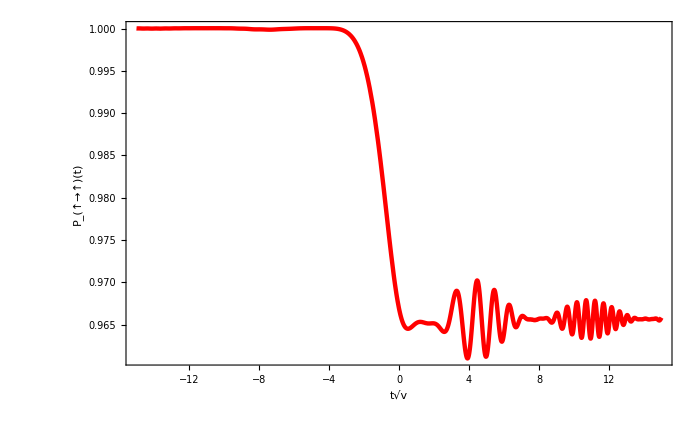

```mathematica
A1=Plot[{probability1[t]},{t,-15,15},PlotRange->All,Axes->None,  Frame->True,FrameLabel->{"t√v","P_(↑→↑)(t)","",""}, ImageSize->700,PlotStyle->{{Red,Thickness[0.0045]},{Black,Thickness[0.004], Dashing[Large]},{Blue,Thickness[0.004]},{Blue,Thickness[0.004]},{Red,Thickness[0.004]},{Red,Thickness[0.004]}},LabelStyle->{FontFamily->"Times New Roman",34,GrayLevel[0]},FrameStyle->{{Black,Black},{Black,Black}}]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb,array,mathtools,color}","\\DeclarePairedDelimiter\\bra{\\langle}{\\rvert}", "\\DeclarePairedDelimiter\\ket{\\lvert}{\\rangle}"},Magnification->2.5];
SetOptions[LinTicks,MajorTickLength->{0.03,0},MinorTickLength->{0.013,0}];
MaTeX["{\\color{blue} \\text{Caley-Klein parameters}\\color{black}}"]
```

-Graphics-

```mathematica
(*-Graphics-*)

Prob1[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=Abs[c[t,t0,A,A0,ω,Δ,D1,0]]^2;

Prob2[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=Abs[d[t,t0,A,A0,ω,Δ,D1,0]]^2;

(*-Graphics-*)

c[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=a3[t,t0,A,A0,ω,Δ,D1,k] (a1[t,t0,A,A0,ω,Δ,D1,k] a2[t,t0,A,A0,ω,Δ,D1,k]-b1[t,t0,A,A0,ω,Δ,D1,k] Conjugate[b2[t,t0,A,A0,ω,Δ,D1,k]])-(a1[t,t0,A,A0,ω,Δ,D1,k] b2[t,t0,A,A0,ω,Δ,D1,k]+b1[t,t0,A,A0,ω,Δ,D1,k] Conjugate[a2[t,t0,A,A0,ω,Δ,D1,k]]) Conjugate[b3[t,t0,A,A0,ω,Δ,D1,k]];

d[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=(a1[t,t0,A,A0,ω,Δ,D1,k] b2[t,t0,A,A0,ω,Δ,D1,k]+b1[t,t0,A,A0,ω,Δ,D1,k] Conjugate[a2[t,t0,A,A0,ω,Δ,D1,k]]) Conjugate[a3[t,t0,A,A0,ω,Δ,D1,k]]+b3[t,t0,A,A0,ω,Δ,D1,k] (a1[t,t0,A,A0,ω,Δ,D1,k] a2[t,t0,A,A0,ω,Δ,D1,k]-b1[t,t0,A,A0,ω,Δ,D1,k] Conjugate[b2[t,t0,A,A0,ω,Δ,D1,k]]);

(*-Graphics-*)

a1[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=-(ⅈ Gamma[ⅈ delta3[A,A0,ω,Δ,D1,k]+1])/(√(2π))(ParabolicCylinderD[-ⅈ delta3[A,A0,ω,Δ,D1,k],x[t+(D1+k ω-ω0)]]ParabolicCylinderD[-ⅈ delta3[A,A0,ω,Δ,D1,k]-1,y[t0+(D1+k ω-ω0)]]+ParabolicCylinderD[-ⅈ delta3[A,A0,ω,Δ,D1,k],y[t+(D1+k ω-ω0)]]ParabolicCylinderD[-ⅈ delta3[A,A0,ω,Δ,D1,k]-1,x[t0+(D1+k ω-ω0)]]);

b1[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=(Gamma[ⅈ delta3[A,A0,ω,Δ,D1,k]+1]Exp[-ⅈ π/4])/(√(2π delta3[A,A0,ω,Δ,D1,k]))(ParabolicCylinderD[-ⅈ delta3[A,A0,ω,Δ,D1,k],x[t+(D1+k ω-ω0)]]ParabolicCylinderD[-ⅈ delta3[A,A0,ω,Δ,D1,k],y[t0+(D1+k ω-ω0)]]-ParabolicCylinderD[-ⅈ delta3[A,A0,ω,Δ,D1,k],y[t+(D1+k ω-ω0)]]ParabolicCylinderD[-ⅈ delta3[A,A0,ω,Δ,D1,k],x[t0+(D1+k ω-ω0)]])Exp[ⅈ ψ1[t,A,A0,ω,ω0, ϕ,Δ,D1,k]];


a2[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=-(ⅈ Gamma[ⅈ delta2[A,A0,ω,Δ,D1,k]+1])/(√(2π))(ParabolicCylinderD[-ⅈ delta2[A,A0,ω,Δ,D1,k],x[t+(D1+k ω)]]ParabolicCylinderD[-ⅈ delta2[A,A0,ω,Δ,D1,k]-1,y[t0+(D1+k ω)]]+ParabolicCylinderD[-ⅈ delta2[A,A0,ω,Δ,D1,k],y[t+(D1+k ω)]]ParabolicCylinderD[-ⅈ delta2[A,A0,ω,Δ,D1,k]-1,x[t0+(D1+k ω)]]);

b2[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=(Gamma[ⅈ delta2[A,A0,ω,Δ,D1,k]+1]Exp[-ⅈ π/4])/(√(2π delta2[A,A0,ω,Δ,D1,k]))(ParabolicCylinderD[-ⅈ delta2[A,A0,ω,Δ,D1,k],x[t+(D1+k ω)]]ParabolicCylinderD[-ⅈ delta2[A,A0,ω,Δ,D1,k],y[t0+(D1+k ω)]]-ParabolicCylinderD[-ⅈ delta2[A,A0,ω,Δ,D1,k],y[t+(D1+k ω)]]ParabolicCylinderD[-ⅈ delta2[A,A0,ω,Δ,D1,k],x[t0+(D1+k ω)]])Exp[ⅈ ψ2[t,A,A0,ω,ω0, ϕ,Δ,D1,k]];

a3[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=-(ⅈ Gamma[ⅈ delta1[A,A0,ω,Δ,D1,k]+1])/(√(2π))(ParabolicCylinderD[-ⅈ delta1[A,A0,ω,Δ,D1,k],x[t+(D1+k ω+ω0)]]ParabolicCylinderD[-ⅈ delta1[A,A0,ω,Δ,D1,k]-1,y[t0+(D1+k ω+ω0)]]+ParabolicCylinderD[-ⅈ delta1[A,A0,ω,Δ,D1,k],y[t+(D1+k ω+ω0)]]ParabolicCylinderD[-ⅈ delta1[A,A0,ω,Δ,D1,k]-1,x[t0+(D1+k ω+ω0)]]);

b3[t_,t0_,A_,A0_,ω_,Δ_,D1_,k_]:=(Gamma[ⅈ delta1[A,A0,ω,Δ,D1,k]+1]Exp[-ⅈ π/4])/(√(2π delta1[A,A0,ω,Δ,D1,k]))(ParabolicCylinderD[-ⅈ delta1[A,A0,ω,Δ,D1,k],x[t+(D1+k ω+ω0)]]ParabolicCylinderD[-ⅈ delta1[A,A0,ω,Δ,D1,k],y[t0+(D1+k ω+ω0)]]-ParabolicCylinderD[-ⅈ delta1[A,A0,ω,Δ,D1,k],y[t+(D1+k ω+ω0)]]ParabolicCylinderD[-ⅈ delta1[A,A0,ω,Δ,D1,k],x[t0+(D1+k ω+ω0)]])Exp[ⅈ ψ3[t,A,A0,ω,ω0, ϕ,Δ,D1,k]];

(*-Graphics-*)

delta1[A_,A0_,ω_,Δ_,D1_,k_]:=(A0/(4 √α)BesselJ[k,A/ω])(A0/(4 √α)BesselJ[k,A/ω]);

delta2[A_,A0_,ω_,Δ_,D1_,k_]:=(Δ/(2 √α)BesselJ[k,A/ω])(Δ/(2 √α)BesselJ[k,A/ω]);

delta3[A_,A0_,ω_,Δ_,D1_,k_]:=(A0/(4 √α)BesselJ[k,A/ω])(A0/(4 √α)BesselJ[k,A/ω]);

x[t_]:=t Exp[-3ⅈ π/4];

y[t_]:=t  Exp[ⅈ π/4];

(*-Graphics-*)

ψ1[t_,A_,A0_,ω_,ω0_, ϕ_,Δ_,D1_,k_]:=(omega1[ω,ω0,D1,k])^2/2+ϕ;

ψ2[t_,A_,A0_,ω_,ω0_, ϕ_,Δ_,D1_,k_]:=(omega2[ω,ω0,D1,k])^2/2;

ψ3[t_,A_,A0_,ω_,ω0_, ϕ_,Δ_,D1_,k_]:=(omega3[ω,ω0,D1,k])^2/2-ϕ;

(*-Graphics-*)

omega1[ω_,ω0_,D1_,k_]:=D1+k ω-ω0;

omega2[ω_,ω0_,D1_,k_]:=D1+k ω;

omega3[ω_,ω0_,D1_,k_]:=D1+k ω+ω0;
```

```mathematica
(*-Graphics-*)
Grid11=Table[{t,Prob1[t,-50,A,A0,ω,Δ,D1,0]},{t,-5,5,0.2}]; (*-Graphics-*)
```

```mathematica
A1=ListPlot[Grid11,PlotRange->All,Axes->None,  Frame->True,FrameLabel->{"ϵ_0/√v","P_(↑→↑)(∞)","",""}, ImageSize->700,PlotMarkers->{-Graphics-,0.04},PlotStyle->{{Black,Thickness[0.005], Dashing[Large]},{Red,Thickness[0.007]},{Red,Thickness[0.005]}},LabelStyle->{FontFamily->"Times New Roman",34,GrayLevel[0]},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->{FontFamily->"Times New Roman",34,GrayLevel[0]},FrameStyle->{{Black,Black},{Black,Black}}]
```

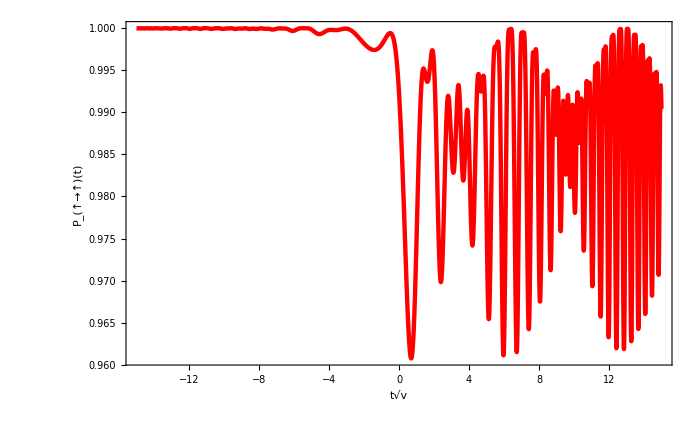

```mathematica
B1=Plot[Prob1[t,-50,A,A0,ω,Δ,D1,0],{t,-5,15},PlotRange->All,Axes->None,  Frame->True,FrameLabel->{"t√v","P_(↑→↑)(t)","",""}, ImageSize->700,PlotStyle->{{Red,Thickness[0.0045]},{Black,Thickness[0.004], Dashing[Large]},{Blue,Thickness[0.004]},{Blue,Thickness[0.004]},{Red,Thickness[0.004]},{Red,Thickness[0.004]}},LabelStyle->{FontFamily->"Times New Roman",34,GrayLevel[0]},FrameStyle->{{Black,Black},{Black,Black}}]
```